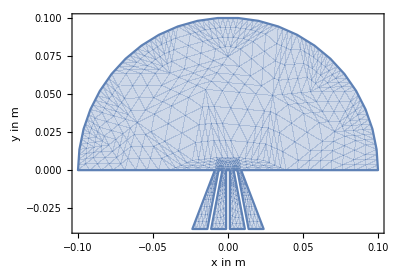

{1.29191,Null}

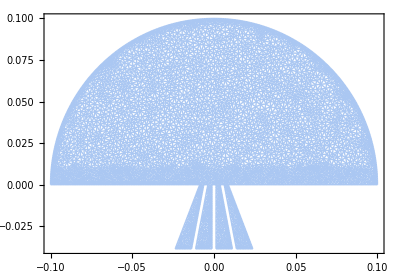

{1.19357,Null}

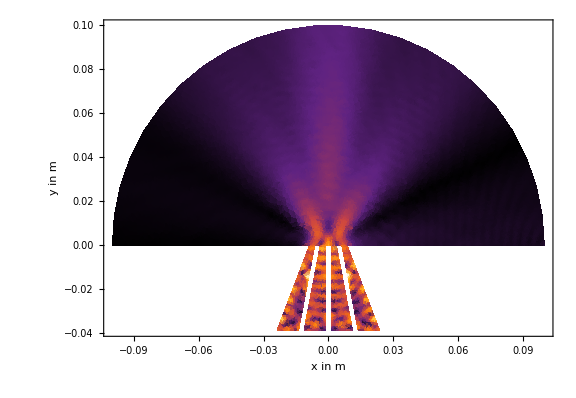

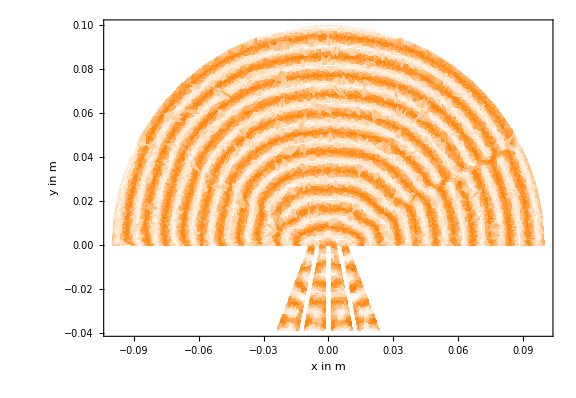

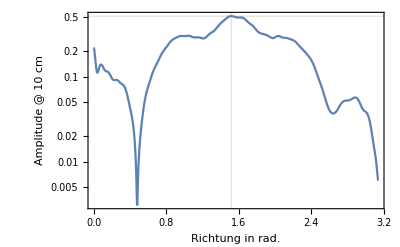

```mathematica
Needs["NDSolve`FEM`"]

(*Konstanten*)
c = 343;
f = 40000;
ρ = 1.225;
(*resultierend*)
ω = N[2 Pi f];
λ =N[ c/f];
T =N[1/f] ;

(*Problem definition*)
reg=Disk[{0,0},0.1,{0,π}]; (*region*)
bc=NeumannValue[-(I ω)/(ρ c)*p[x,y],y>0]; (*boundary Condition*)

Module[{n=4,depth= 4.5λ ,distance =0.005,holeDia,transDia = 0.01,transDist},
holeDia =distance/2;
transDist=distance-holeDia+transDia;
Do[
reg = RegionUnion[reg,
Polygon[{
{i*distance-holeDia/2,0},{i*distance+holeDia/2,0},
{i*transDist+transDia/2,-depth},{i*transDist-transDia/2,-depth}
}] 
];
bc+=NeumannValue[-(I ω)/(ρ c)*(p[x,y]+2),y==-depth&& i*transDist-transDia/2<x<i*transDist+transDia/2];
,{i,-(n-1)/2,(n-1)/2}]
]
RegionPlot[reg,AspectRatio->Automatic,]

(*Mesh generation*)
mesh=ToElementMesh[reg,
MaxCellMeasure->λ^2/15,
"MaxBoundaryCellMeasure"->λ/8,
"BoundaryMeshGenerator"->{"BoundaryDiscretizeRegion","SamplePoints"->200},
MeshQualityGoal->"Maximal",
MeshRefinementFunction-> Function[{vertices,area},
(Mean[vertices][[2]]<0.01 && area>λ^2/40)
],
"MeshOrder"->2
];//Timing
MeshRegion[mesh,,PlotTheme->"Lines"]

(*Solve Model*)
pde={-(ω^2 p[x,y])/(c^2 ρ)+Div[({{-1/ρ, 0}, {0, -1/ρ}}).Grad[p[x,y],{x,y}],{x,y}]==bc};pfun=NDSolveValue[pde,p,{x,y}∈mesh];//Timing
(*visulize*)
DensityPlot[
Norm[pfun[x,y]],
{x,y}∈reg,
,
ColorFunction->"SunsetColors",
,
PlotPoints->50,
ImageSize->Large
]
DensityPlot[
Arg[pfun[x,y]],
{x,y}∈reg,
,
ColorFunction->(Blend[{Orange,White},Norm[(#*2-1)]]&),
,
PlotPoints->30,
ImageSize->Large
]
Module[{max},
max=NMaximize[Norm[pfun[0.1Cos[θ],0.1 Sin[θ]]],{θ,0,Pi},Method->{"RandomSearch","SearchPoints"->50}];
LogPlot[
Norm[pfun[0.1Cos[θ],0.1 Sin[θ]]],{θ,0,Pi},
Frame->True,
GridLines->{{max[[2,1,2]]},{max[[1]]}},
FrameTicks->{{Automatic,{max[[1]]}},{Automatic,{{max[[2,1,2]],ToString[max[[2,1,2]]*180/Pi]<>"°"}}}},
FrameLabel->{"Richtung in rad.", "Amplitude @ 10 cm"}
]
]
```